# Distribution of rotational velocities

What we observe is “vsini” instead of v (the equatorial rotational speed)

First work to Deconvolve (disentangle, unfold), Chandrasekhar & Muench 1950
-Graphics-

```mathematica
-Graphics-
-Graphics-
```

## Preliminariedades

```mathematica
ClearAll["Global`*"] (*Reset all the variables*)
SetDirectory[NotebookDirectory[]]
```

/home/jurados/OCEAN2025/Proyect

```mathematica
meshgrid[x_List,y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]};
```

The MATLAB function meshgrid generates coordinate matrices from coordinate vectors, primarily used to define a 2-D or 3-D grid for evaluating functions over a grid or making surface plots. Given vectors  x and y,
[X,Y] = meshgrid(x,y) 
returns matrices X and Y of the same size, where each row of X is a copy of vector x and each column of Y is a copy of vector y. 
This creates a grid of points (X(i,j),Y(i,j)) in the Cartesian plane defined by all combinations of elements in x and y. 
This is useful for evaluating functions at all points in the grid for visualization or computation.

### reading and analysing the data

```mathematica
datosgeneve=Flatten@Import["data/alphaPer/vsini.dat"];
```

```mathematica
Length@datosgeneve
```

57

```mathematica
vsini= datosgeneve;
```

```mathematica
Length@vsini
```

57

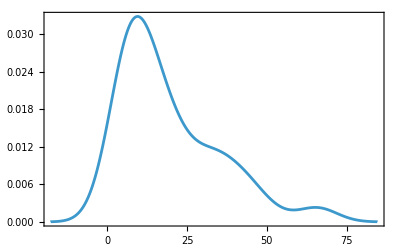

```mathematica
SmoothHistogram[vsini,Frame->True,Axes->True]
```

```mathematica
(*kdeplus=SmoothKernelDistribution[vsini,Automatic,{"Bounded",{0,100},"Gaussian"}];
kdenegs=SmoothKernelDistribution[-vsini,Automatic,{"Bounded",{0,100},"Gaussian"}];*)
kdeplus=SmoothKernelDistribution[vsini];
kdenegs=SmoothKernelDistribution[-vsini];
```

```mathematica
kde = ProbabilityDistribution[PDF[kdeplus, x]-PDF[kdenegs,x],{x,0,100}];
```

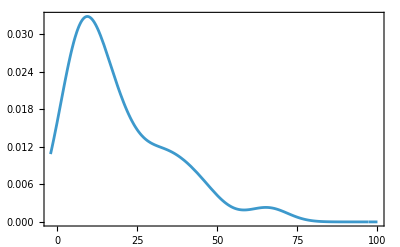

```mathematica
Plot[PDF[kdeplus,x],{x,-2,100},Frame->True]
```

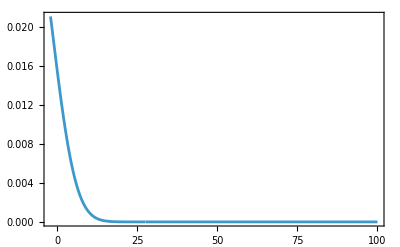

```mathematica
Plot[PDF[kdenegs,x],{x,-2,100},Frame->True, PlotRange->All]
```

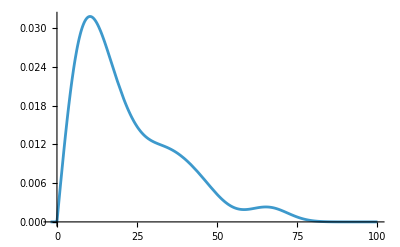

```mathematica
Plot[PDF[kde,x], {x,-2,100}]
```

## Generacion de la Grilla(t,s)

Construction of the matrix A , see followting paper: https://www.aanda.org/articles/aa/pdf/2016/11/aa29070-16.pdf
see Eq. 3,which corresponds to the linearization of:
-Graphics-->  Y = A.X

```mathematica
n=150;
a=0.01;
b=100.;
ds = (b-a)/n;    
c= a + ds/2;
d=b;
dt = (d-c)/n;
t=c+dt (Range[n]-0.5);
s=a+ds (Range[n]-0.5);
```

```mathematica
{T,S}=meshgrid[t,s];
```

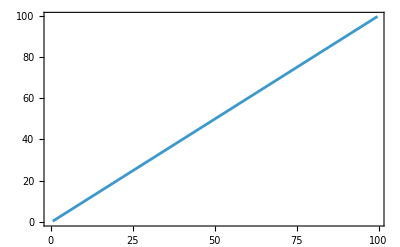

```mathematica
ListLinePlot[{t,s}ᵀ,Frame->True]
```

```mathematica
Correlation[t,s]
```

1.

## The matrix A, which is the design matrix

```mathematica
alphas = Range[-0.5, 2.0, 0.1] //Chop
```

{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
A=dt*Chop[Re[S^(2*#+1)/(T ^(2*#+1)*Sqrt[(T^2-S^2)])]] & /@ alphas;
```

```mathematica
Dimensions@A
```

{26,150,150}

### The density (PDF) of the projected velocities

```mathematica
t;
```

```mathematica
fy=PDF[kde,#]&/@ t;
```

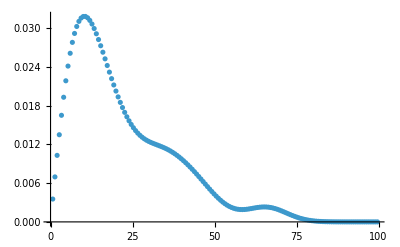

```mathematica
ListPlot[{t,fy}ᵀ]
```

## Estimation of fx (“true velocity”)

Knowing fy and the matrix A, we can find fx (=velsTrue) using Tikhonov regularisation

```mathematica
TamañoAlphas = Length@alphas;
```

```mathematica
velsTrue = Fit[{A[[#]],fy},FitRegularization->{"Tikhonov",1.}] & /@ Range[TamañoAlphas];
```

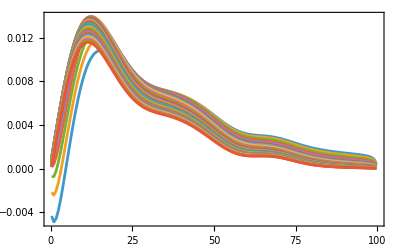

```mathematica
ListLinePlot[Table[Transpose[{s,velsTrue[[k]]}],{k,1,TamañoAlphas}],PlotRange->{{0,100},All},Frame->True]
```

#### Normalización

```mathematica
fxFunList=Interpolation[{t,#}ᵀ]&/@velsTrue ;
```

```mathematica
cteList=NIntegrate[#[x],{x,0.01,100.}]&/@fxFunList;
```

InterpolatingFunction::dmvali: The integration endpoint 0.01 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 100. in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 0.01 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmvali will be suppressed during this calculation.

```mathematica
fxPDFintnorList=MapThread[Interpolation[{t,(#1/#2)}ᵀ]&,{velsTrue,cteList}];
```

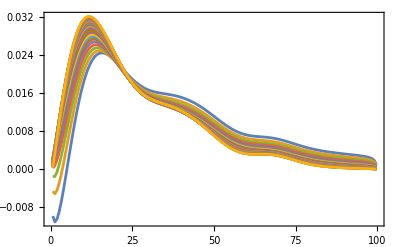

```mathematica
ListLinePlot[Table[Transpose[{t,fxPDFintnorList[[i]][t]}],{i,Length[fxPDFintnorList]}],PlotRange->{{0,100},All},Frame->True,PlotStyle->ColorData[97]/@Range[Length[fxPDFintnorList]]]
```

### Recovery of fy

-Graphics-

```mathematica
Clear[x,y]
```

```mathematica
(*fyes=Table[NIntegrate[(y/(x(x^2-y^2)^(1/2))fxPDFint[x])/.y->t[[k]],{x,t[[k]]+0.00001,t[[k+1]]}],{k,1,Length[t]-1}]*)
```

```mathematica
fyesall=ParallelTable[NIntegrate[((y ^(2*alphas[[#]] + 1))/(x^(2*alphas[[#]] + 1 ) * (x^2-y^2)^(1/2))fxPDFintnorList[[#]][x])/.y->s[[k]],{x,s[[k]],100}],{k,Length[s]}] &/@Range[Length@alphas];
```

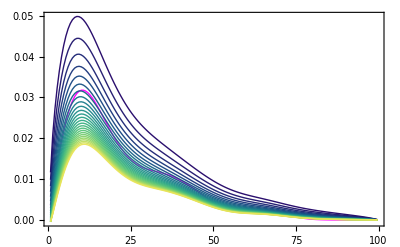

```mathematica
cd=ColorData["BlueGreenYellow"];
minA=Min[alphas];
maxA=Max[alphas];

fyPlot=ListLinePlot[Transpose[{t,fy}],PlotStyle->{Magenta,Thick},PlotRange->All];

fyesPlots=Table[ListLinePlot[Transpose[{t,fyesall[[i]]}],PlotStyle->{Directive[cd[(alphas[[i]]-minA)/(maxA-minA)],Opacity[0.95],Thick]},PlotRange->All,Axes->False,Frame->False],{i,Length[alphas]}];

combined=Show[fyPlot,Evaluate[fyesPlots],PlotRange->All,Frame->True,Axes->False];

colorbar=BarLegend[{cd,{minA,maxA}},LegendLabel->Style[α,14],LegendMarkerSize->{20,200},LabelStyle->Directive[12],LegendFunction->(Framed[#,RoundingRadius->4,FrameMargins->2]&)];

Legended[combined,Placed[colorbar,Right]]
```

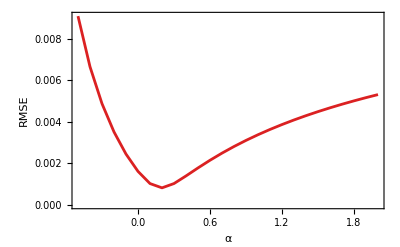

```mathematica
diffList=Chop[Sqrt[Total[(fy-fyesall[[#]])^2]/n] & /@ Range[Length@alphas]];
ListLinePlot[Table[Transpose[{alphas[[i]],diffList[[i]]}],{i,Length[alphas]}],PlotRange->All,Frame->True,FrameLabel->{"α","RMSE"},PlotStyle->ColorData["Rainbow"]/@Range[Length[alphas]]]
```

## BootStap

```mathematica
nmuestra=Length@vsini
```

11818

```mathematica
nbootS=500;
```

```mathematica
muestrasBS=RandomChoice[vsini,{nbootS,nmuestra}];
```

```mathematica
Dimensions@muestrasBS
```

{500,11818}

```mathematica
distsBS= SmoothKernelDistribution[#]& /@muestrasBS;
```

```mathematica
fysBS= PDF[#,t]&/@distsBS;
```

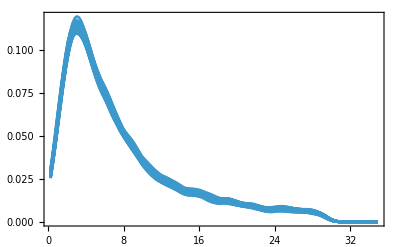

```mathematica
Show[ListLinePlot[{t,#}ᵀ]&/@fysBS[[1;;100]],PlotRange->All,Frame->True]
```

```mathematica
velsTrueBS=Fit[{A,#},FitRegularization->{"Tikhonov",.5}]&/@fysBS;
```

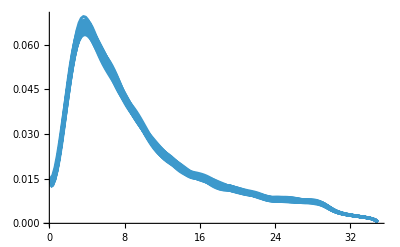

```mathematica
Show[ListLinePlot[{s,#}ᵀ]&/@velsTrueBS[[1;;100]],PlotRange->All]
```

```mathematica
Length@t
```

150

```mathematica
velsTrueBS[[All,1]]
```

```mathematica
quants=Table[Quantile[velsTrueBS[[All,k]],{.025,.975}],{k,Length@s}];
```

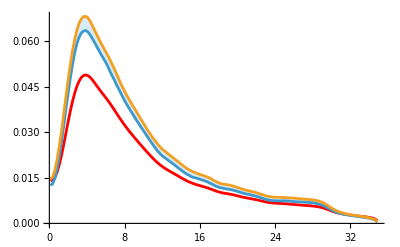

```mathematica
Show[ListLinePlot[{s,velsTrue}ᵀ,PlotStyle->Red],ListLinePlot[{{s,quants[[All,1]]}ᵀ,{s,quants[[All,2]]}ᵀ},Frame->True,Filling->{1->{2}}],PlotRange->All]
```

FALTA NORMALIZAR (Tarea: REVISAR Y NORMALIZAR)

```mathematica
Select[vsini,#==0&]//Length
```

133

## Trick

```mathematica
kde1=SmoothKernelDistribution[vsini];
```

```mathematica
kde2=SmoothKernelDistribution[-vsini];
```

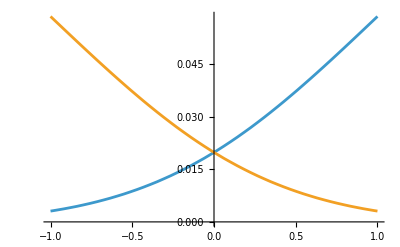

```mathematica
Plot[{PDF[kde1,x],PDF[kde2,x]},{x,-1,1}]
```

```mathematica
kde3=ProbabilityDistribution[PDF[kde1,x]-PDF[kde2,x],{x,0,35}];
```

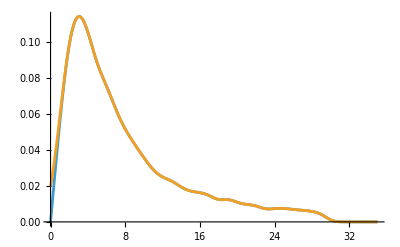

```mathematica
Plot[{PDF[kde3,x],PDF[kde1,x]},{x,0,35}]
```

```mathematica
fy=PDF[kde3,#]&/@ s;
```

Knowing fy and the matrix A, we can find fx (=velsTrue) using Tikhonov

```mathematica
velsTrue=Fit[{A,fy},FitRegularization->{"Tikhonov",.1}];
```

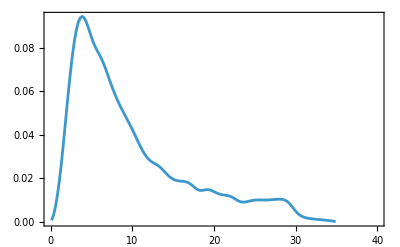

```mathematica
ListLinePlot[{s,velsTrue}ᵀ,PlotRange->{{0,40},All},Frame->True]
```

#### Normalización

```mathematica
fxPDFint=Interpolation[{s,velsTrue}ᵀ]
```

InterpolatingFunction[…]

```mathematica
cte=NIntegrate[fxPDFint[x],{x,.36,34.6}]
```

0.943261

```mathematica
fxPDFintnor=Interpolation[{s,velsTrue/cte}ᵀ];
```

```mathematica
NIntegrate[fxPDFintnor[x],{x,.36,34.6}]
```

1.

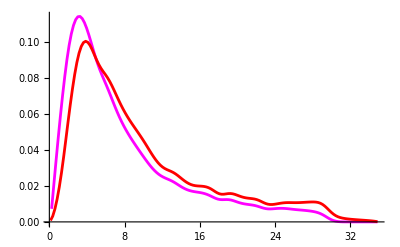

```mathematica
Show[ListLinePlot[{t,fy}ᵀ,PlotStyle->Magenta],ListLinePlot[{s,fxPDFintnor[s]}ᵀ,PlotStyle->Red],PlotRange->All]
```

### Recovery of fy

-Graphics-

```mathematica
Clear[x,y]
```

```mathematica
(*fyes=Table[NIntegrate[(y/(x(x^2-y^2)^(1/2))fxPDFint[x])/.y->t[[k]],{x,t[[k]]+0.00001,t[[k+1]]}],{k,1,Length[t]-1}]*)
```

```mathematica
fyes=ParallelTable[NIntegrate[(y/(x(x^2-y^2)^(1/2))fxPDFintnor[x])/.y->t[[k]],{x,t[[k]],34.7}]//Quiet,{k,Length[t]}];
```

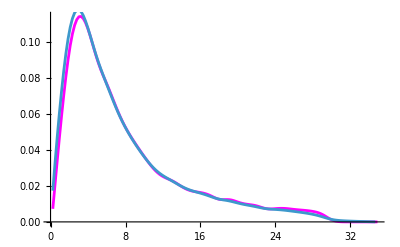

```mathematica
Show[ListLinePlot[{t,fy}ᵀ,PlotStyle->Magenta],ListLinePlot[{t,fyes}ᵀ]]
```